# helper

```mathematica
getBlack[s_]:=StringCases[s,("B<< Monte-Carlo "~~Shortest[__]~~" total games: "~~(x:DigitCharacter..)~~WordBoundary):>ToExpression[x]/10^6];
getWhite[s_]:=StringCases[s,("W<< Monte-Carlo "~~Shortest[__]~~" total games: "~~(x:DigitCharacter..)~~WordBoundary):>ToExpression[x]/10^6]
```

```mathematica
ClearAll[makePlot];
makePlot[expr_->data_]:=
Module[{all},
all=Join[getBlack[data],getWhite[data]];
all=all;ListLinePlot[{Legended[Style[Take[all,Length[getBlack[data]]],Black],Placed["Black",Below]],Legended[Style[Drop[all,Length[getBlack[data]]],LightGray],Placed["White",Below]]},PlotLabel->StringTrim[expr,"\\"]];
ListLinePlot[{getWhite[data],getBlack[data]},Mesh->All,PlotLabel->Style[StringTrim[expr,"\\"],Medium],PlotRange->All,PlotMarkers->{Automatic,8},ImageSize->Scaled[0.18],PlotStyle->{LightGray,Black}]]
```

```mathematica
?PlotMarkers
```

PlotMarkers is an option for graphics functions like ListPlot and ListLinePlot that specifies what markers to draw at the points plotted.

## MPI

```mathematica
SetDirectory[NotebookDirectory[]];
rawdata=Map[FileNameSplit[#][[2]]->Import[#,"Text"]&,FileNames["MPI*/gtg_output.txt","mpi"]];
```

```mathematica
data=Normal@Map[Function[{val},StringJoin[Last/@val]],GroupBy[rawdata,StringJoin[Riffle[Most[StringSplit[First[#],"_"]]," "]]&]]
```

{MPI 12 vs 1→648832,MPI 12 vs 2→669319,MPI 12 vs 4→747819,MPI 12 vs 8→765237,MPI 2 vs 1→548879,MPI 4 vs 1→580699,MPI 4 vs 2→600692,MPI 8 vs 1→601230,MPI 8 vs 2→609912,MPI 8 vs 4→665102}
 |  |  |  |

```mathematica
Length[data]
```

10

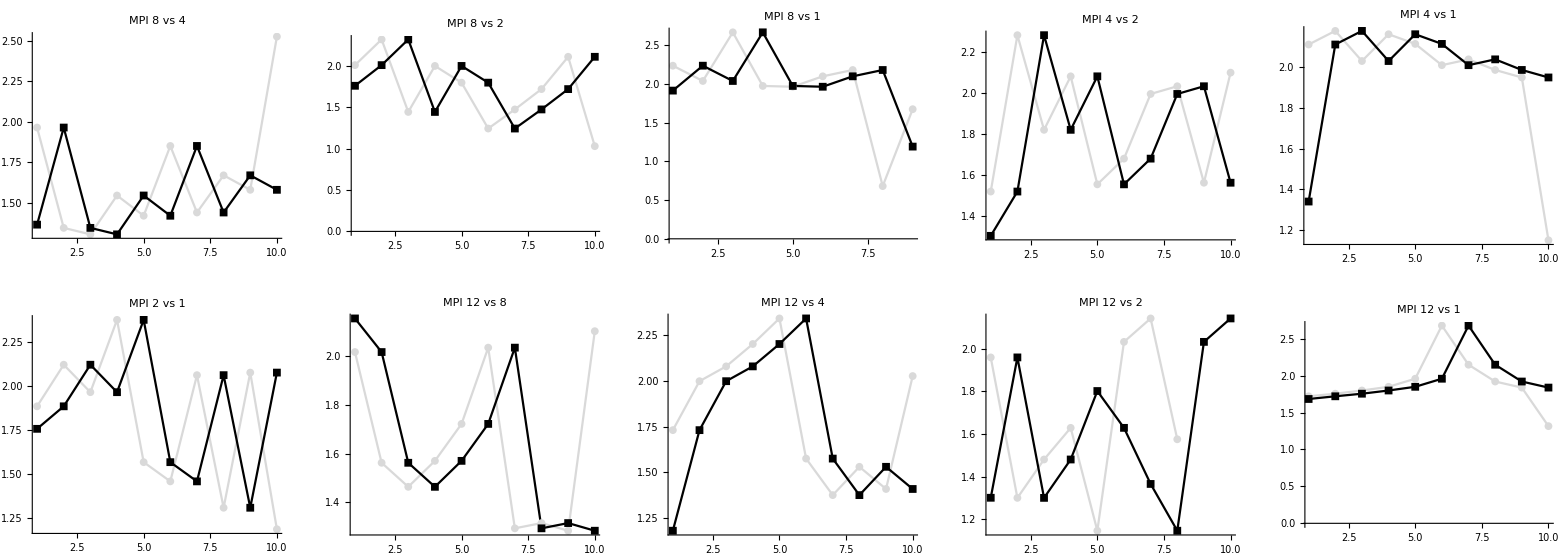

```mathematica
GraphicsGrid[Partition[makePlot/@Reverse@Sort@Normal[data],5],ImageSize->Scaled[2],ImagePadding->Scaled[0.2]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"stev_1sec_MPI_vs.pdf"}],GraphicsGrid[Partition[makePlot/@Reverse@Sort@Normal[data],5],ImageSize->Scaled[2],ImagePadding->Scaled[0.2]]]
```

C:\Users\adakk\Desktop\mpi_omp\cs484-master\data\final\1sec\setv_1sec_MPI_vs.pdf

## OMP

```mathematica
SetDirectory[NotebookDirectory[]];
rawdata=Map[FileNameSplit[#][[2]]->Import[#,"Text"]&,FileNames["OMP*/gtg_output.txt","omp"]];
Length[rawdata]
```

100

```mathematica
data=Normal@Map[Function[{val},StringJoin[Last/@val]],GroupBy[rawdata,StringJoin[Riffle[Most[StringSplit[First[#],"_"]]," "]]&]];
```

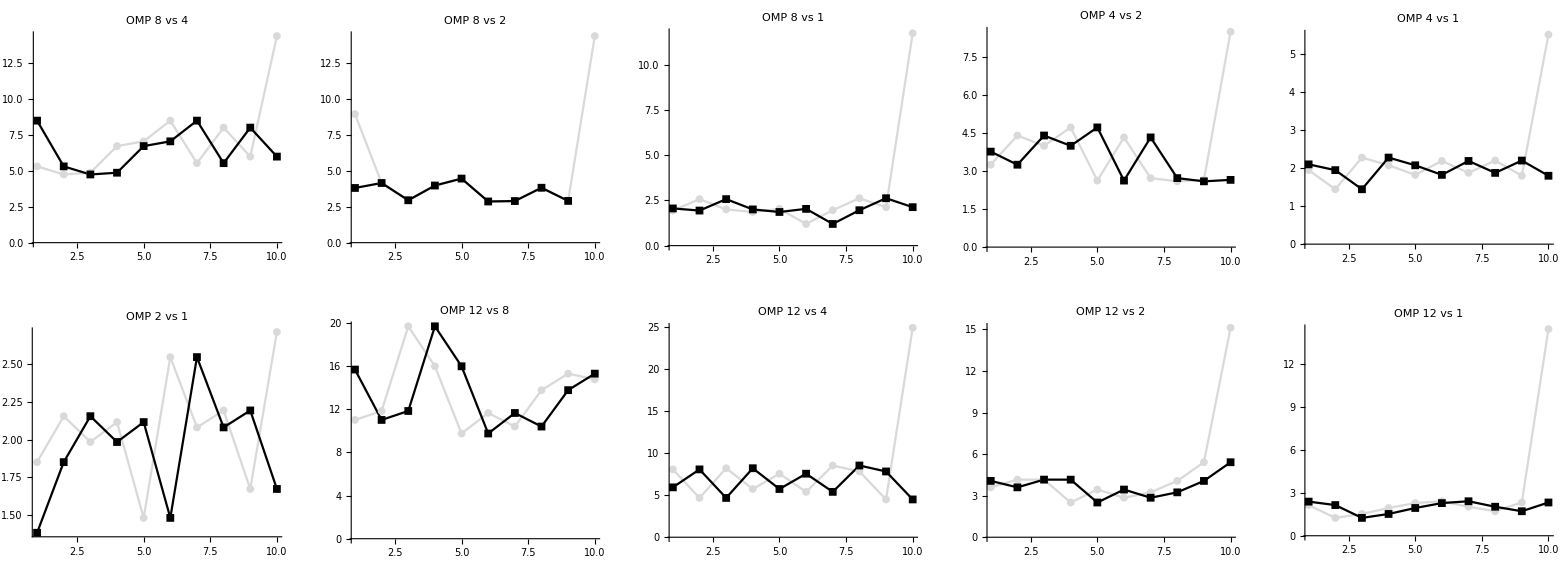

```mathematica
GraphicsGrid[Partition[makePlot/@Reverse@Sort@Normal[data],5],ImageSize->Scaled[1],ImagePadding->Scaled[0.1]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"stev_1sec_OMP_vs.pdf"}],GraphicsGrid[Partition[makePlot/@Reverse@Sort@Normal[data],5],ImageSize->Scaled[2],ImagePadding->Scaled[0.2]]]
```

C:\Users\adakk\Desktop\mpi_omp\cs484-master\data\final\1sec\stev_1sec_OMP_vs.pdf